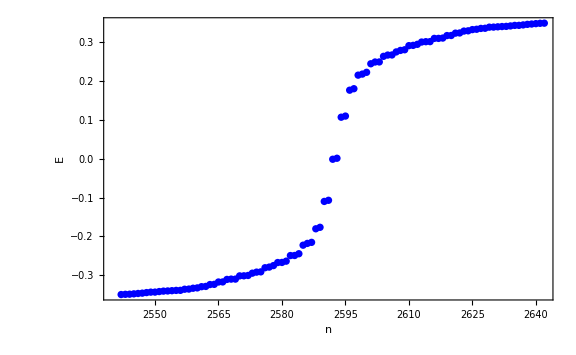

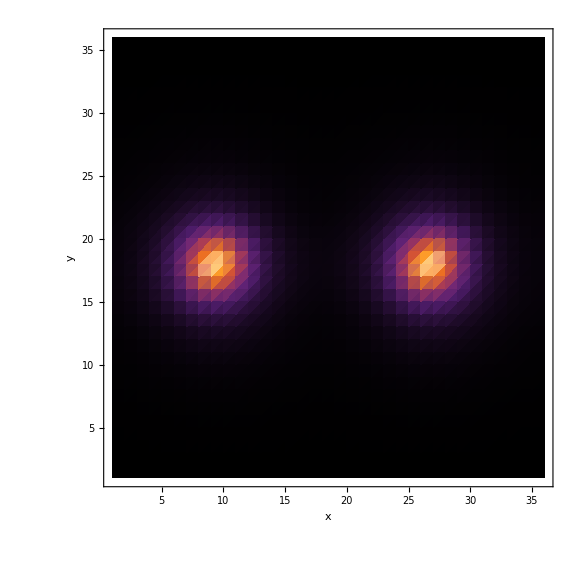

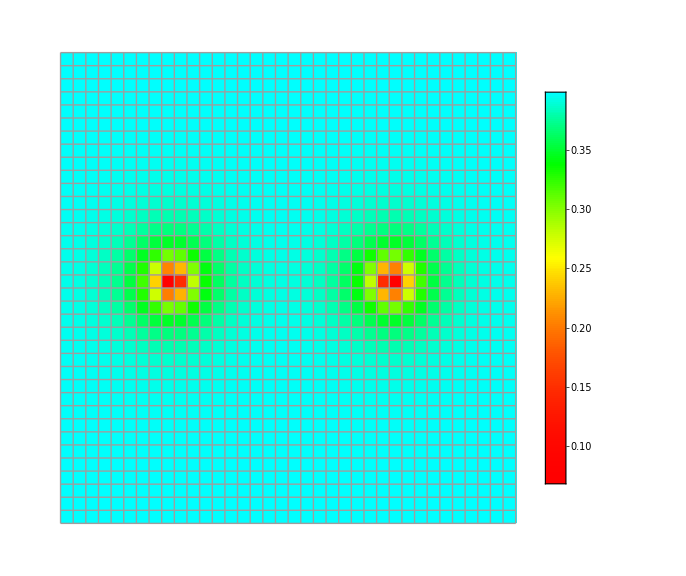

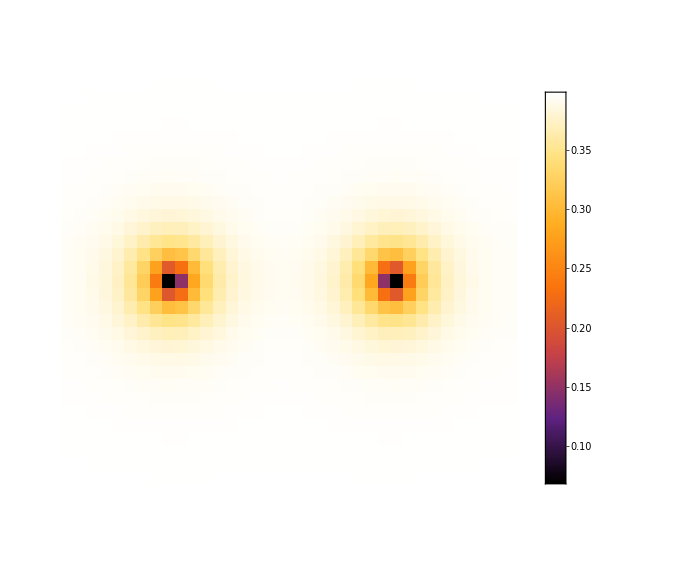

```mathematica
SetDirectory[NotebookDirectory[]];
xn=yn=36;(*格点大小*)
energy = Import["eigval.dat"];
del = Flatten[Import["order_module.dat"]];
vals=ListPlot[energy[[Round[Length[energy]/2]-50;;Round[Length[energy]/2]+50]],PlotStyle->Directive[Blue],ImageSize->Large,Frame->True,FrameLabel->{"n","E"},Frame->True,FrameStyle->Directive[Black,FontSize->20,FontFamily->"Times New Roman"]]
del2=ArrayReshape[del,{xn,yn}];
Export["del.dat",del2];
Position[del2,n_/;n<(Min[del2]+0.1)];(*Vortex position*)
vortex=ListDensityPlot[del2,PlotRange->All,FrameStyle->Directive[Black,24,FontFamily->"Times New Roman"],ColorFunction->ColorData[{"SunsetColors","Reverse"}],ImageSize->Large,PlotRange->{{1,xn},{1,yn}},FrameLabel->{Style["x"],"y"}]
ArrayPlot[del2,ColorFunction->(Hue[#^2/2]&),PlotLegends->Automatic,PlotTheme->"Detailed",ImageSize->Large,Mesh->All]
ArrayPlot[del2,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotTheme->"Detailed",ImageSize->Large]
Export["vortex.png",vortex,ImageSize->1000];
Export["vals.png",vals,ImageSize->1000];
```